# Machine precision approximation to series solutions using Bernstein polynomials.

Spyros Don Travlos

Solutions to differential equations can be approximated by series with the terms of the series being calculated via recursion formulas. Unfortunately these algorithms (the recursions) are rarely of practical use in evaluating the series solution as they run into numerical precision problems. This is due to the limitations of floating point arithmetic, as presently implemented in modern processors. This paper demonstrates that by solving the recursion by the use of high precision arithmetic, the series solution can be accurately evaluated. This solution can then be approximated by Bernstein polynomials. This approximation to the original problem uses only machine precision.

## Introduction

This paper will present a method of approximating differential equations, using a novel method. The method relies on the use of high precision arithmetic, to which Mathematica is ideally suited. Of course, there are other languages that can handle high precision arithmetic such as Python^1.
A basic outline of the method is to start by expanding all the coefficients in the differential equation into polynomials. Then a series solution Σ c_n x^n is substituted the recursion formula for the  c_n is generated by matching coefficients in x^n.  In general this prescription leads to a formal solution. A number of factors need to be taken into account, for example whether the coefficients are continuous, whether there are singularities in the coefficients, and the accuracy with which the coefficients have been approximated. This paper is not claiming that any and all differential equations can be approximated by this technique. Also, there are numerous numerical techniques for solving DEs and PDEs. By way of example what is presented here is a solution of the radial Schrödinger equation for the F-F molecule using a potential energy function defined by a sum of even-tempered Gaussian functions.^2 So it is a real practical example, but one that illustrates the difficulties associated with the method.^3 The quantum mechanical problem can be split into three equations, the only equation that is difficult to solve is the radial equation given by:

(∂^2 Ψ)/(∂r^2)+ℏ^2/μ(W-U(r) +(J(J+1))/r^2)Ψ=0

where r is positive; J is the rotational eigenvalue number and U(r) is the potential energy function defined as a function of r the distance between the two atoms.

The potential energy is represented by a sum of tempered Gaussian functions^3

U(r) = a_0 ⅇ^(-α r^2)+ a_1 ⅇ^(-α β  r)+ a_2 ⅇ^(-α (β  r)^2)+ a_3 ⅇ^(-α β^3 r^2)+ a_4 ⅇ^(-α β^4 r^2)

To this end we define the following function:

```mathematica
gaussG[J_,r_]:=Block[{α=6/10,β=179/100,a0=-915059/100000000,a1=-11127505/10000000,a2=323325687/100000000,a3=224888398/100000000,a4=2309621497/100000000}, (a0 Exp[-α r^2]+a1 Exp[-α β r^2]+a2 Exp[-α (β r)^2]+a3 Exp[-α β ^3r^2]+a4 Exp[-α β ^4r^2])+J(J+1)/r^2]
```

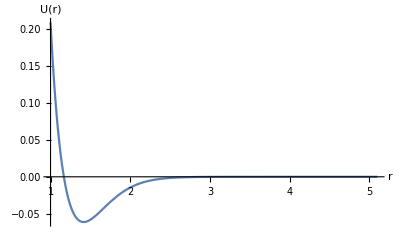

```mathematica
Plot[gaussG[0,r],{r,1,5.1},AxesLabel->{r ,"U(r)"},PlotRange->All]
```

This is the problem that will be tackled in this paper. It will quickly become apparent that the method requires very high precision arithmetic to converge. In spite of this, it will be shown that this solution can be approximated with machine precision and thus a massive speed up is achieved.
Solving differential equations via a series solution is highly intuitive, and immediately gives a recursion formula, which defines the solution. Unfortunately these recursions often require very high precision arithmetic to allow for the calculation of the series solution.
By using a Bernstein polynomial approximation to the series solution, an approximation is obtained that can be calculated using only machine precision arithmetic. The protocol is as follows: Find the recursion formula/algorithm that solves the (P)DE, then use high precision arithmetic to generate an approximation that can be calculated using only machine precision arithmetic.

## Description of the method

The equation has a regular singularity at r = 0 if J≠0. For the purposes of this paper assume J = 0. That is, the system is in the lowest rotational energy state. If we make the substitution:

y = ⅇ^-r

where y ∈ [0,1]

This is a useful transformation to make because by substituting Σ c_n y^n, the series will converge quickly.  Making this transformation of the dependent variable, the radial Schrödinger equation with J = 0 becomes:

y^2(∂^2 Φ)/(∂y^2)+y(∂ Φ)/(∂y)+ℏ^2/μ(W-V(y) )Φ=0

where V(y) is the potential energy defined above in terms of the variable y. This equation has a regular singularity at zero.

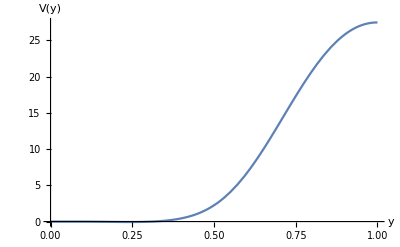

```mathematica
Plot[ gaussG[0,Log[y]],{y,0,1},AxesLabel->{y,"V(y)"}]
```

Now V(y) is approximated as a polynomial in y. To achieve this, use will be made of the Jacobi orthogonal polynomials^4.  The polynomials are defined by the following function:

```mathematica
g[n_,p_,q_,y_]:=((q+n-1)!)/((p+2 n-1)!)∑_(m=0)^n (-1)^m Binomial[n,m]   ((p+2 n-m-1)!)/((q+n-m-1)!)y^(n-m)
```

This defines the Jacobi orthogonal polynomials over [0,1]. The normalization constant is given by the following function:

∫y^(q-1)y^(p-q)g[n,p,q,y]g[m,p,q,y] = (n!(n+q-1)!(n+p-1)!(n+p-q)!)/((2n+p)(((2n+p-1)!)^2)  n=m and 0 if n ≠ m

```mathematica
hn[n_,p_,q_]:=(n!(n+q-1)!(n+p-1)!(n+p-q)!)/((2n+p)((2n+p-1)!)^2)
```

To expand V(y) in terms of Jacobi polynomials would require the evaluation of the following integral:

a_n=∫_0^1 y^(q-1)y^(p-q)g[n,p,q,y]V(y)ⅆy

The expansion is given by:

((2n +p)((2 n +p +1)!)^2)/(n!(n+q-1)!(n+p-1)!(n+p-q)!)∑_(n=0)^∞ a_n g[n,p,q,y]

The series is truncated and the polynomials expanded and subsequently reduced to give a polynomial in y.

This type of intergral equation 5 can be numerically difficult to evaluate, so instead of evaluting it directly, use is made of the fact that g[n,p,q,y] is a polynomial, using p = 4 and q = 1, the polynomial terms are calculated directly. Therefore instead of equation 5, the following integral is evaluated:

∫_0^1 y^(1-1)y^(4-1)y^(n-m)V(y)ⅆy

This expression is then substituted back into the formula for the Jacobi polynomials. In this way the expansion of V(y) as a polynomial in y can be obtained:

```mathematica
Short[Off[General::lrgexp];integralTerm[n_]=Integrate[y^(n-m)(1-y)^(4-1) y^(1-1)gaussG[0,-Log[y]],{y,0,1,1},Assumptions->n>=0&&n∈Integers]]
```

(√(π/15) ((«1»)/(√((«1»)^2))-(«1»)/(√((«1»)^2))+«26»+(«1»)/(√((«1»)^2))))/1281640000000

Substituting this into the definition of Jacobi polynomials gives the coefficients of the expansion a_n:

```mathematica
a[n_,p_,q_]:=((q+n-1)!)/((p+2 n-1)!)∑_(m=0)^n (-1)^m Binomial[n,m] ((p+2n-m-1)!)/((q+n-m-1)!)  integralTerm[n]
```

The error for thirteen terms of the approximation is calculated via errorJacobi:

```mathematica
errorJacobi=Block[{$MaxExtraPrecision=1000},Table[(Sum[(N[a[i,4,1],100]/hn[i,4,1] g[i,4,1,y]),{i,0,13}]-gaussG[0,-Log[y]]),{y,1/10000,1,1/100}]];
```

Notice that extra precision is required to get the calculation to work, plotting the error:

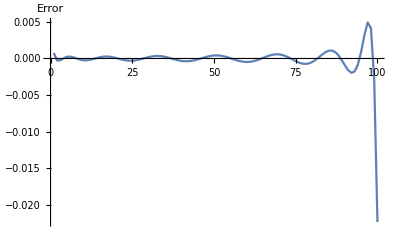

```mathematica
ListPlot[errorJacobi,Joined->True,PlotRange->All,AxesLabel->{None,"Error"}]
```

The approximation is worst at r near 0 or y =1, but given that there are only thirteen terms in the approximation, it is impressive.
Define the approximation to U(r) and V(y):

```mathematica
Short[approx=Block[{$MaxExtraPrecision=1000},ExpandAll[Sum[(N[a[i,4,1],100]/hn[i,4,1] g[i,4,1,y]),{i,0,13}]]/.y->Exp[-r]]]
```

«135»-«127» ⅇ^(-13 r)+«127» ⅇ^(-12 r)-«144» ⅇ^(-11 r)+«9»+«138» ⅇ^(«1»)-«137» ⅇ^(-3 r)+«136» ⅇ^(-2 r)-«135» ⅇ^-r

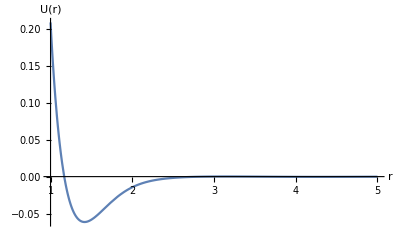

```mathematica
Plot[approx,{r,1,5},AxesLabel->{r,"U(r)"},PlotRange->All]
```

The physical constants for the problem are defined as:

```mathematica
μ=(18.9984032*10^-3)/(6.023*10^23);(*Reduced mass*)
plank=(6.62606957*10^-34/(2*π))^2;(*Planks constant*)
pi=N[Rationalize[(1.60217657*10^-39 μ/plank)/27210.7,0],5000];(*In millihartree*)
```

Take note that the constant pi is defined to 5000 digits! This is needed to make the summation of the series solution possible.. 
Substitution of a series solution  Σ c_n y^(n+m) into equation 3, matching like terms in y gives a recursion formula  of the following form:

c_n=-pi ( d[1] c_(n-1)+d[2] c_(n-2)+d[3] c_(n-3)+d[4] c_(n-4) +d[5] c_(n-5)+d[6] c_(n-6)+d[7] c_(n-7)+d[8] c_(n-8)+d[9] c_(n-9)+d[10] c_(n-10)+d[11] c_(n-11)+d[12] c_(n-12)+d[13]c_(n-13))/(n^2+2 n m)

Using only thirteen terms in the Jacobi expansion means that a set of thirteen constants must be defined for use in the calculation of the  recursion formula:

```mathematica
Table[d[i]=-1000Rationalize[Coefficient[approx,Exp[-r],14-i],0];,{i,1,13}];
```

A function to calculate the recursion is defined:

```mathematica
recursion[d_,pi_,y_,m_?NumericQ]:=Module[{n,sum=1,m1,y1,prevsum =0},
(*Restrict m to be numeric to supresses symbolic computation for Findroot otherwise it
 tries symbolic first*)
	m1=Rationalize[m];
	y1=Rationalize[y];
	Do[c[n]=0,{n,1,12}];
	c[13]=1;n=14;
	While[Abs[prevsum-sum]>10^-16,{
		n=n+1;
   c[14]=-pi Sum[d[i] c[i],{i,1,13}]/((n-14)^2+2*(n-14)*m1);
		prevsum=sum;		
		sum=sum+c[14] y1^(n-14);
		Do[c[k]=c[k+1],{k,1,13}];
}
];
sum ]
```

The initial value of c_0 is 0.  The function runs until the sum no longer changes by 10^-16 . The boundary conditions of the equation are Φ(0) = 0 and Φ(1) = 0. The series that was substituted into the equation was y^m∑_(n=0)^∞ c_n y^n, accordingly the boundary condition at y = 0 is satisfied.

The recursion gives the values of c_nwhich are functions of m. The expression ∑_(n=0)^∞ c_n =  0 is the other boundary condition. If truncated it is a polynomial in m. The roots of this polynomial define the eigenvalues of the problem. So m is directly related to the energy levels of this particular quantum mechanical problem. The correct value of m ensures that Φ(1) = 0. To this end, an eigenvalue of the system is found as follows: (Note because of the huge number for the precision this calculation is slow.)

```mathematica
eigenvalue = z /.FindRoot[recursion[d,pi,1,z],{z,3/2,2},AccuracyGoal->32,WorkingPrecision->30000];
recursion[d,pi,1,eigenvalue]
```

-1.94824497542840369839175503746039149079265372091563101343789887422460258964153888093713995776847326451936655338276025224780844634887971959745562517185054741088643213771320009790269841501×10^-79

A study of the recursion formula shows that as n gets large c_nis approximated by Max[d[1], ..., d[13]]^n/(n!)^2; so as n gets large c_n→0 .

```mathematica
N[Max[Table[Abs[d[i]],{i,1,13}]]]
```

3.6591×10^9

In this case the numerator of c_n is growing as 10^(9n), while the denominator is growing as  (n!)^2. Eventually the factorial term will dominate and c_n_-> 0 as n gets large. Unfortunately the c_n need to be summed, however values of the c_nare very large, consider n = 10 then the numerator is 10^90if the sign of c_nis changing, which it must do for  Σ c_n = 0 to be true. Precision is lost extremely quickly in the value of the sum, if there are less than 90 digits of precision. 

This presents a quandary: an easy formula for calculating the solution has been obtained and it converges, but it requires high precision arithmetic, which is slow and memory intensive. If the number of Jacobi polynomials used to approximate V(y) is increased the problem will get even worse. This is a pity as it was fairly easy to find the expansion of V(y), and then to generate the recursion. Furthermore the series solution provided good intuition about the problem. The recursion formula is an algorithm for solving the problem, but in practice it is difficult to use. 

Clearly there are other ways for solving this problem, so the question can be asked why not just use one of them? The point being made is that in some sense this “formal” solution of the problem is easy and quick to derive. It suits human thinking, unlike just using a black box numerical method or trying to invent one for the particular problem. Series solutions can work for a range of problems including PDEs and even non-linear equations. Unfortunately, as in this example, real world problems present this precision problem. As will be shown in the next section, the solution can be approximated accurately with Bernstein polynomials. This then gives a solution that uses only machine precision.

### Checking the Solution

A plot of the solution for the eigenvalue found above is (Note: It is slow so skip it if needed) as follows:

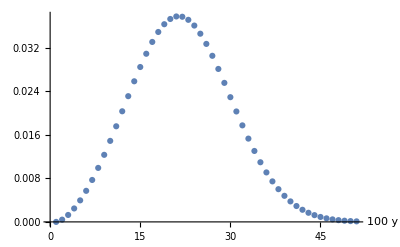

```mathematica
ListPlot[ParallelTable[y^eigenvalue recursion[d,pi,y,eigenvalue],{y,0,0.5,1/100},Method->"FinestGrained"],AxesLabel->{100y,None}]
```

Now define two functions to approximate the first and second derivatives of this solution:

```mathematica
firstD[y_]:=(*First derivative*)Block[{dy=.001,m=eigenvalue},((y+dy)^m recursion[d,pi,y+dy,m]-(y-dy)^m recursion[d,pi,y-dy,m])/(2 dy)]
```

```mathematica
secondD[y_]:=(*Second Derivative*)Block[{dy=.001,m=eigenvalue},((y+dy)^m recursion[d,pi,y+dy,m]-2 y^m recursion[d,pi,y,m]+(y-dy)^m recursion[d,pi,y-dy,m])/ dy^2]
```

The equation being solved is equation 3 where  the energy W =-m^2/pi-  the constant coefficient in the expansion of V(y). Defining a function to calculate the error:

```mathematica
recursionerror=ParallelTable[(y^2 secondD[y]+y firstD[y])+y^eigenvalue recursion[d,pi,y,eigenvalue]( -eigenvalue^2+0.000773444299836383535192656-1000 pi gaussG[0,-Log[y]]),{y,0.01,1,.1},Method->"FinestGrained"]
```

{-0.0000711114,-0.00326599,-0.00588124,-0.00130488,-0.000427214,-1.94937×10^-6,2.85805×10^-8,4.57725×10^-10,3.85364×10^-11,1.01656×10^-12}

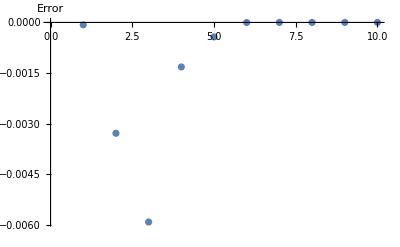

```mathematica
ListPlot[recursionerror,AxesLabel->{None,"Error"}]
```

Therefore the solution generated by the recursion formula approximates the differential equation equation 3.

## Approximation by Bernstein Polynomials

The n^th Bernstein polynomial of a function f(x) is defined^5 as f[x] = ∑_(k=0)^n f[k/n] Binomial[n, k] (x^k(1-x))^(n-k) . Bernstein polynomials have the advantage that convergence is uniform and not pointwise. To check whether this results in a better approximation to the potential energy for this problem, than the one achieved using Jacobi polynomials, the following  function is defined:

```mathematica
approxBernstein[n_]:=∑_(k=0)^n (gaussG[0,r]/.r->-Log[k/n]) Binomial[n,k] y^k(1-y)^(n-k)
```

Now plotting the error using 1000 terms of this approximation.

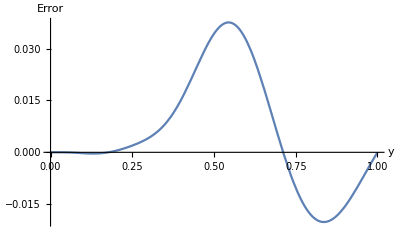

```mathematica
Plot[approxBernstein[1000]-gaussG[0,-Log[y]],{y,0,1},AxesLabel->{y,"Error"}]
```

The maximum error is .04, whereas in the case of the  Jacobi expansion the maximum error after only 13 terms was 0.02 as opposed to 1000 terms the Bernstein approximation. Having tried to get a better approximation to the potential energy, the idea is abandoned and discussion reverts to the main topic of this paper.

The idea is to use the Bernstein polynomials to approximate the series solution that was previously generated using the recursion formula. The advantage of Bernstein polynomials is that they are guaranteed to fit the first and second derivatives. Since the objective is to fit the solution to a differential equation of second order this is an important property. To this end redefine approxBernstein to approximate the series solution instead of the potential energy V(y):

```mathematica
approxBernstein[y_]=Block[{n=100},SetPrecision[ParallelSum[recursion[d,pi,k/n,eigenvalue]Binomial[n,k] y^k(1-y)^(n-k),{k,0,n}],MachinePrecision]];
```

This is a 100 term polynomial approximation to the solution of the original differential equation. The extra code, is to force Mathematica^6 to use machine precision. The following function for the error is defined:

```mathematica
bernsteinerror=With[{cmuopt=SystemOptions["CatchMachineUnderflow"]},Internal`WithLocalSettings[SetSystemOptions["CatchMachineUnderflow"->False],ParallelTable[(z^2 D[z^SetPrecision[eigenvalue,MachinePrecision] approxBernstein[z],{z,2}]/.z->y)+(z D[z^SetPrecision[eigenvalue,MachinePrecision] approxBernstein[z],z]/.z->y)+(z^SetPrecision[eigenvalue,MachinePrecision] approxBernstein[z]/.z->y)*( -SetPrecision[eigenvalue,MachinePrecision]^2-1000. SetPrecision[pi,MachinePrecision]gaussG[0,-Log[y]]),{y,0.0001,1.,.1}],SetSystemOptions[cmuopt]]]
```

{-4.86134×10^-10,-0.00590259,0.0381888,-0.0817896,-0.255987,-0.108521,-0.00812774,-0.0000678576,3.8335×10^-8,4.12763×10^-11}

The error is worse than using the series solution on its own, but this is machine precision approximation so memory usage is decreased and speed is greatly increased.

Next the impact of increasing the number of terms of the Bernstein approximation is tested: (Note: The next line takes a significant amount of time.)

```mathematica
approxBernstein[y_]=Block[{n=1000},SetPrecision[ParallelSum[recursion[d,pi,k/n,eigenvalue]Binomial[n,k] y^k(1-y)^(n-k),{k,0,n},Method->"FinestGrained"],MachinePrecision]];
```

This results in a much improved approximation:

```mathematica
bernsteinerror=With[{cmuopt=SystemOptions["CatchMachineUnderflow"]},Internal`WithLocalSettings[SetSystemOptions["CatchMachineUnderflow"->False],ParallelTable[(z^2 D[z^SetPrecision[eigenvalue,MachinePrecision] approxBernstein[z],{z,2}]/.z->y)+(z D[z^SetPrecision[eigenvalue,MachinePrecision] approxBernstein[z],z]/.z->y)+(z^SetPrecision[eigenvalue,MachinePrecision] approxBernstein[z]/.z->y)*( -SetPrecision[eigenvalue,MachinePrecision]^2-1000. SetPrecision[pi,MachinePrecision]gaussG[0,-Log[y]]),{y,0.0001,1.,.1}],SetSystemOptions[cmuopt]]]
```

{-6.20597×10^-10,-0.00335588,0.000283381,-0.012686,-0.0215496,-0.00404484,-0.0000719939,-6.58714×10^-8,1.59918×10^-10,1.30595×10^-13}

As would be expected, the error is significantly better with 1000 terms. The following table presents some timing and memory usage statistics. The calculations were run on a Mac Pro 2013 3.7 GHz Quad Core Xeon X5 20GB DDR3 RAM using only one core. The calculations show the results of calculating 100 or 1000 points of the solution for the “formal” method using just the recursion formula or the approximation using Bernstein polynomials.

Number of Solution Points | Absolute Timing /seconds | Memory Usage/Bytes□
100 (Series-Recursion) | 2272 | 659448
1000 (Series-Recursion) | 33389 | 2667472
100 (Bernsein) | .032 | 35168
1000 (Bernstein) | 2.7 | 1394048

Table 1: Timing and memory Usage.

## Conclusion

The outline of the method is as follows: If the equation has an independent variable r , r ∈ (-∞,∞) then make the substitution y = 1/(1+r^2), or if r ∈ [0,∞) then make the substitution y = ⅇ^-r. Now approximate all coefficients in the equation, which are not polynomials in y by Jacobi orthogonal polynomials over [0,1]. This results in an equation which has polynomial coefficients. 
Substituting  Σ c_n y^n for 1-D problem or Σ c_ij x^i y^jfor a 2-D problem, it is straight forward to derive the recursion formula that is obeyed by the coefficients c_n or c_iij, by matching like terms in y^n or x^i y^j.  This recursion represents an algorithm for the solution to the equation. Unfortunately as was shown in this paper when a numerical value for the series is attempted it quickly runs into numerical precision problems. The idea is to use the recursion with high precision arithmetic to calculate the series solution accurately, then use Bernstein polynomials to generate an approximation to the solution of the original problem. The Bernstein approximation works with machine precision, so it is fast and not memory intensive. It should be noted that many problems in finance and other fields are represented by differential equations that already have polynomial coefficients. The method outlined in this paper, proceeds from a formal algorithm that solves the problem, to one that works on a machine with limited numerical precision without the need for a detailed knowledge of numerical analysis. 

The series solution forces analysis of the problem: Is it continuous? Is it linear? Is it multi dimensional? And what are the ranges of the variables? This results in a deep intuition of problem.

 Unfortunately the series solution is a “formal” solution, to generate a practical algorithm for usage, use of the recursion is made to generate a number of solution points, which can then be approximated via a Bernstein polynomials. The insights gained from the series solution are considerable, while it is straight forward to generate the Bernstein approximation.

## References

F. Johansson, “mpmath,” “mpmath.org” (05/04/2017). mpmath.org

L. Bytautas, N. Matsunaga, T. Nagata, M. S. Gordon, and K. Ruedenberg, “Accurate ab initio potential energy curve of F_2. III. The vibration rotation spectrum,” The Journal of Chemical Physics, 127, 2007 pp. 204313–204332. DOI: 10.1063/1.2805392.

S. D. Travlos  and J. C. A.. Boeyens, “A new method for approximate solution of one-dimensional Schrödinger equations,” Theoretica Chimica Acta, 87(6), 1994 pp. 453–464. DOI: 10.1007/BF01127808.

M. Abramowitz and I. A. Stegun, (eds) Handbook of Mathematical Functions, 10th ed., Publisher N.Y.: Publisher Dover, 1972.

G. Lorentz, Bernstein Polynomials, 2^nd ed., Publisher New York: Publisher Chelsea, 1986.

R. Oleksandr. “mathemathitca.stackexchange.com.” (01/15/2017) mathematica.stackexchange.com/questions/24857/how-to-flush-machine-underflows-to-zero-and-prevent-conversion-to-arbitrary-prec to use Machine precision numbers.

About the Authors

The author is an independent researcher, with a background in Theoretical Chemistry. Mathematica has been used extensively in the author’s work since its first release. The author has had a varied career spanning, Researcher, Lecturer, Trader, Quantitative Analyst and Treasurer.  Presently he runs a family office. In his spare time he tinkers with Mathematica, and occasionally comes up with things that may be of interest to others.

Spyros Don Travlos
dontravlos@gmail.com